```mathematica
(********************************* Data *****************************)
(* range of μ and ω *)
omega=Table[10^i,{i,-4,4}];
logo=Table[Log[10^i],{i,-4,4}];
massP={1,1.5,2,3,10,50,207,400,900,1836};
(* Nuclear exponents of 1s basis set for different masses and ω *)
m[1]={0.036377,0.036377,0.037689,0.085144,0.577278,5.220210,50.674434,502.112311,5006.657809};
m[2]={0.060120,0.060120,0.061722,0.127792,0.856476,7.794067,75.891419,752.781105,7508.756638};
m[3]={0.084515,0.084515,0.086327,0.169869,1.130886,10.350143,101.049347,1003.262711,10010.263443};
m[4]={0.133343,0.133343,0.135727,0.252075,1.670284,15.430786,151.265259,1503.905487,15012.256622};
m[5]={0.447388,0.447578,0.453301,0.782700,5.316467,50.645339,501.753938,5005.275726,50016.428232};
m[6]={1.722260,1.722260,1.750488,3.323288,25.532837,250.824745,2502.048564,25005.971909,250018.472672};
m[7]={4.733582,4.735107,4.883118,11.928101,104.179688,1035.908413,10352.169991,103506.202698,1035019.111633};
m[8]={7.275696,7.279511,7.615204,21.950836,200.734253,2000.933838,20002.161980,200006.122589,2000018.310547};
m[9]={12.044067,12.051697,13.013001,47.368164,450.780029,4500.905228,45002.138138,450006.122589,4500018.310547};
m[10]={18.414612,18.437500,20.878906,94.456787,918.828125,9180.938721,91802.234650,918006.134033,9180018.615723};

(* double sets of {Logo,exp}*)
setM=Table[{logo[[j]],m[i][[j]]},{i,10},{j,9}];
setMo=Table[{omega[[j]],m[i][[j]]},{i,10},{j,9}];
setMo2=Table[{omega[[j]],m[i][[j]]/massP[[i]]},{i,10},{j,9}];
setEX=Table[{logo[[j]],m[i][[j]]/massP[[i]]},{i,10},{j,9}];
dataM=FlattenAt[setM,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
dataMo=FlattenAt[setMo,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
dataMo2=FlattenAt[setMo2,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
dataEX=FlattenAt[setEX,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
```

```mathematica
(* simple form: exp=1/2*mp*ω *)
expSIM=Table[N[1/2 *massP[[i]]*omega[[j]]],{i,10},{j,9}];
setSIM=Table[{omega[[j]],expSIM[[i]][[j]]},{i,10},{j,9}];
diff=Table[expSIM[[i]]-m[i],{i,10}];
setdiff=Table[{logo[[j]],diff[[i]][[j]]},{i,10},{j,9}];
```

```mathematica
(* simple EX-form: exp=1/2*ω *)
expSIMex=Table[N[1/2 *omega[[j]]],{j,9}];
setSIMex=Table[{omega[[j]],expSIMex[[j]]},{j,9}];
diffex=Table[expSIMex[[j]]-setEX[[i]][[j]][[2]],{i,10},{j,9}];
diffexper=Table[(expSIMex[[j]]-setEX[[i]][[j]][[2]])/(setEX[[i]][[j]][[2]])*100,{i,10},{j,9}];
setdiffex=Table[{logo[[j]],diffex[[i]][[j]]},{i,10},{j,9}];
setdiffexper=Table[{logo[[j]],diffexper[[i]][[j]]},{i,10},{j,9}];
```

```mathematica
(********************************* Plotting *****************************)
```

```mathematica
listplotM=Table[Transpose[{logo,m[i]}],{i,10}];
listplotEX=Table[Transpose[{logo,m[i]/massP[[i]]}],{i,10}];
```

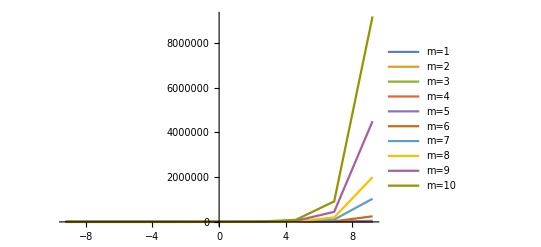

```mathematica
(* m-included exponents in different omegas *)
ListLinePlot[Table[listplotM[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

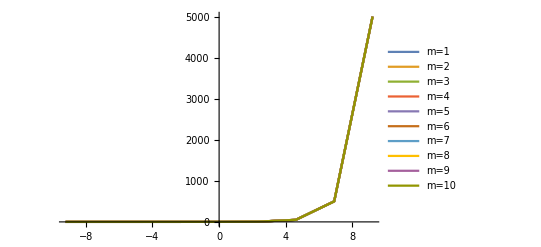

```mathematica
(* m-excluded exponents in different omegas *)
ListLinePlot[Table[listplotEX[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

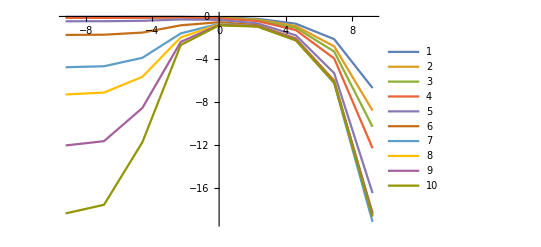

```mathematica
(* plotting difference between simple form data and true exponents *)
ListLinePlot[Table[setdiff[[i]],{i,10}],PlotLegends->Automatic,PlotRange->All]
```

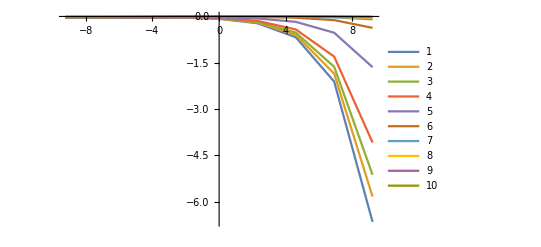

```mathematica
(* plotting difference between ex-simple form data and true ex-exponents *)
ListLinePlot[Table[setdiffex[[i]],{i,10}],PlotLegends->Automatic,PlotRange->All]
```

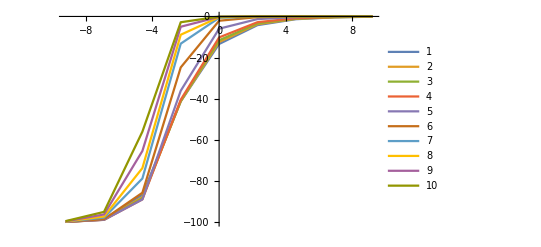

```mathematica
(* plotting percentage error between ex-simple form data and true ex-exponents *)
ListLinePlot[Table[setdiffexper[[i]],{i,10}],PlotLegends->Automatic,PlotRange->All]
```

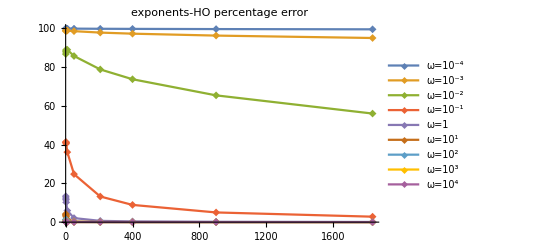

```mathematica
(********************************* Harmonic Oscillator wave function *****************************)
For[j=1,j<10,j++,HO[j]=Table[N[(massP[[i]]*omega[[j]])/2],{i,10}]];
For[j=1,j<10,j++,o[j]=Table[m[i][[j]],{i,10}]];
listplotHO=Table[Transpose[{massP,Abs[(HO[j]-o[j])/o[j]*100]}],{j,9}];
(* percentage error for nuclear exponents vs harmonic oscillator exponents *)
ListLinePlot[Table[listplotHO[[i]],{i,9}],PlotRange->All,PlotLegends->{"ω=10^-4","ω=10^-3","ω=10^-2","ω=10^-1","ω=1","ω=10^1","ω=10^2","ω=10^3","ω=10^4"},PlotMarkers->{"◆", 8},PlotLabel->Framed[Style["exponents-HO percentage error",Red,14]]]
```

FittedModel[1.94755 ⅇ^(0.999991 (4.47244+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.94755 | 4.25955 | 0.457221 | 0.648652
b | 0.999991 | 0.767315 | 1.30323 | 0.195933
c | 4.47244 | 8.29562 | 0.539133 | 0.591172

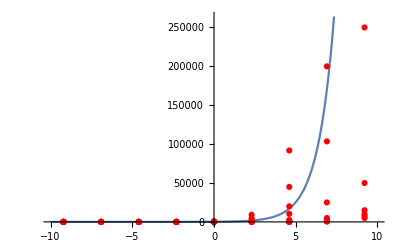

```mathematica
(********************************* Fitting: Subscript[m, p]-included exponents *****************************)
fitM=NonlinearModelFit[dataM,{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fitM["ParameterTable"]
Show[{Plot[fitM[x],{x,-10,10}],ListPlot[dataM,PlotStyle->Red]}]
```

FittedModel[0.909796 ⅇ^(0.998687 (-0.585954+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.909796 | 0.000548632 | 1658.3 | 3.24583×10^-18
b | 0.998687 | 0.000127945 | 7805.57 | 2.98452×10^-22
c | -0.585954 | 0.000498487 | -1175.46 | 2.55884×10^-17

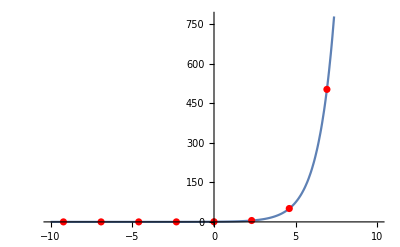

```mathematica
(* mp=1 *)
fit1M=NonlinearModelFit[setM[[1]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fit1M["ParameterTable"]
Show[{Plot[fit1M[x],{x,-10,10}],ListPlot[setM[[1]],PlotStyle->Red]}]
```

FittedModel[0.538266 ⅇ^(0.999654 (2.23312+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.538266 | 0.000219162 | 2456.02 | 3.07547×10^-19
b | 0.999654 | 0.000045966 | 21747.7 | 6.38011×10^-25
c | 2.23312 | 0.000117927 | 18936.5 | 1.46387×10^-24

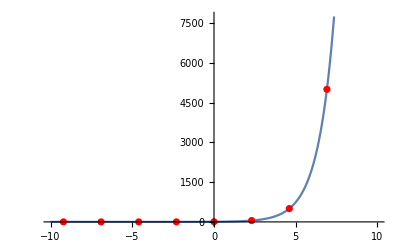

```mathematica
(* mp=10 *)
fit5M=NonlinearModelFit[setM[[5]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fit5M["ParameterTable"]
Show[{Plot[fit5M[x],{x,-10,10}],ListPlot[setM[[5]],PlotStyle->Red]}]
```

FittedModel[2.81603 ⅇ^(0.999984 (5.78712+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.81603 | 0.0000373958 | 75303.3 | 3.70186×10^-28
b | 0.999984 | 7.91824×10^-6 | 126289. | 1.66387×10^-29
c | 5.78712 | 0.000105306 | 54955.4 | 2.45042×10^-27

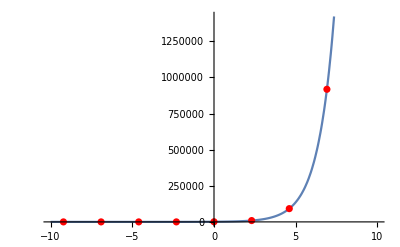

```mathematica
(* mp=1836 *)
fit10M=NonlinearModelFit[setM[[10]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fit10M["ParameterTable"]
Show[{Plot[fit10M[x],{x,-10,10}],ListPlot[setM[[10]],PlotStyle->Red]}]
```

{a→0.000244325}

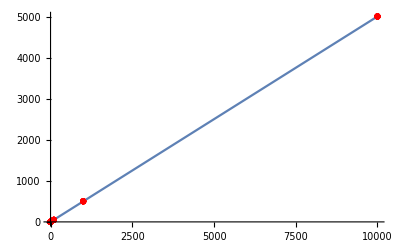

```mathematica
(* fitting simple form: mp=1 & 1836 *)
fitMsim=FindFit[dataMo2,(1/2+a)*x,{a},x]
Show[{Plot[(1/2+a)*x/.fitMsim,{x,0,10^4}],ListPlot[dataMo2,PlotStyle->Red]}]
```

{a→0.000244325}

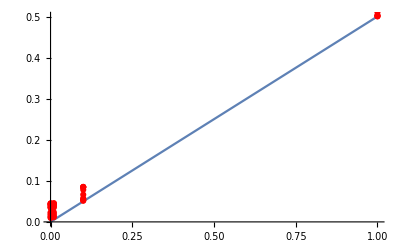

```mathematica
fitMsim=FindFit[dataMo2,(1/2+a)*x,{a},x]
Show[{Plot[(1/2+a)*x/.fitMsim,{x,0,1}],ListPlot[dataMo2,PlotStyle->Red]}]
```

{a→0.000680725}

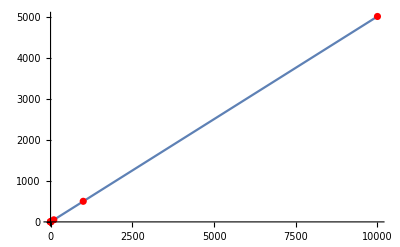

```mathematica
fitMsim1=FindFit[setMo2[[1]],(1/2+a)*x,{a},x]
Show[{Plot[(1/2+a)*x/.fitMsim1,{x,0,10^4}],ListPlot[setMo2[[1]],PlotStyle->Red]}]
```

{a→0.000168043}

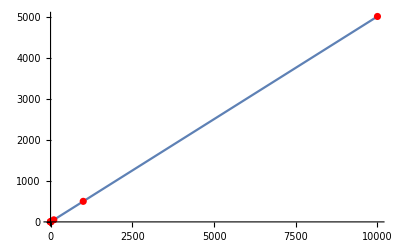

```mathematica
fitMsim5=FindFit[setMo2[[5]],(1/2+a)*x,{a},x]
Show[{Plot[(1/2+a)*x/.fitMsim5,{x,0,10^4}],ListPlot[setMo2[[5]],PlotStyle->Red]}]
```

{a→1.03813×10^-6}

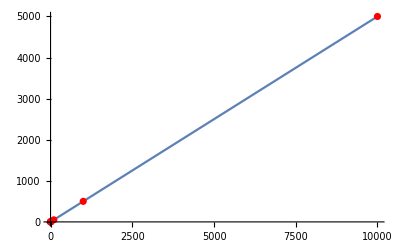

```mathematica
fitMsim10=FindFit[setMo2[[10]],(1/2+a)*x,{a},x]
Show[{Plot[(1/2+a)*x/.fitMsim10,{x,0,10^4}],ListPlot[setMo2[[10]],PlotStyle->Red]}]
```

```mathematica
(* percentage error for simple form: 1/2*a*m*ω *)
a1=0.000244;
sim[x_]:=(1/2+a1)*x;
simdata=Table[sim[omega[[i]]],{i,9}];
pererr=Table[Abs[simdata[[j]]-m[i][[j]]/massP[[i]]]/(m[i][[j]]/massP[[i]])*100,{i,10},{j,9}];
simfinal=Table[simdata[[j]]*massP[[i]],{i,10},{j,9}];
simpererr2=Table[Abs[simfinal[[i]][[j]]-m[i][[j]]]/(m[i][[j]])*100,{i,10},{j,9}];
simdiff2=Table[simfinal[[i]][[j]]-m[i][[j]],{i,10},{j,9}];
simdiff2set=Table[{logo[[j]],simdiff2[[i,j]]},{i,10},{j,9}];
simdiff2data=FlattenAt[simdiff2set,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
simpererrdataM=FlattenAt[simpererr2,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
```

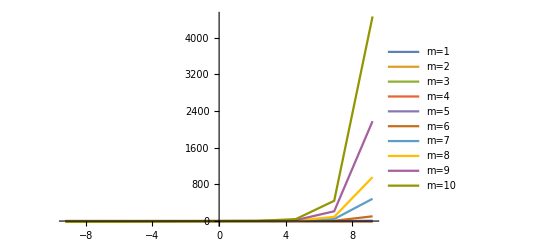

```mathematica
ListLinePlot[Table[simdiff2set[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

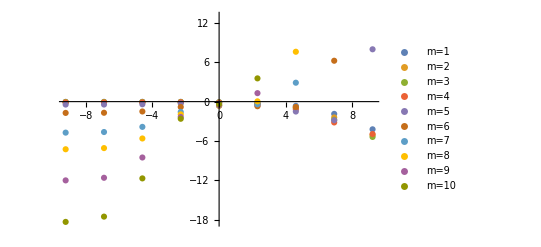

```mathematica
ListPlot[Table[simdiff2set[[i]],{i,10}],PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

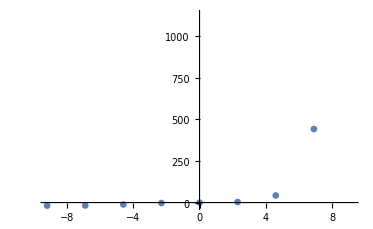

```mathematica
ListPlot[simdiff2set[[10]]]
```

```mathematica
a1=0;
sim[x_]:=(1/2+a1)*x;
simdata=Table[sim[omega[[i]]],{i,9}];
pererr=Table[Abs[simdata[[j]]-m[i][[j]]/massP[[i]]]/(m[i][[j]]/massP[[i]])*100,{i,10},{j,9}];
simfinal=Table[simdata[[j]]*massP[[i]],{i,10},{j,9}];
simpererr2=Table[Abs[simfinal[[i]][[j]]-m[i][[j]]]/(m[i][[j]])*100,{i,10},{j,9}];
simdiff2=Table[m[i][[j]]-simfinal[[i]][[j]],{i,10},{j,9}];
simdiff2set=Table[{logo[[j]],simdiff2[[i,j]]},{i,10},{j,9}];
simdiff2setM=Table[{massP[[i]],simdiff2[[i,j]]},{i,10},{j,9}];
simdiff2setMM=Table[Transpose[{massP,Transpose[simdiff2][[j]]}],{j,9}];

simdiff2dataM=FlattenAt[simdiff2setM,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
simdiff2data=FlattenAt[simdiff2set,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
simpererrdataM=FlattenAt[simpererr2,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
ListPlot[Table[simdiff2set[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

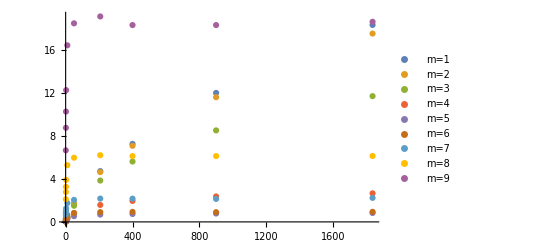

```mathematica
ListPlot[simdiff2setMM,PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

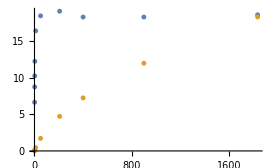

```mathematica
ListPlot[{simdiff2setMM[[9]],simdiff2setMM[[1]]}]
```

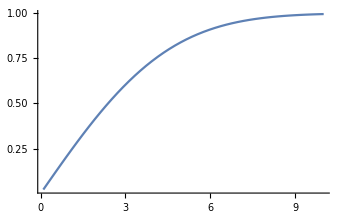

```mathematica
Plot[Erf[0.2x],{x,0.1,10},PlotRange->All]
```

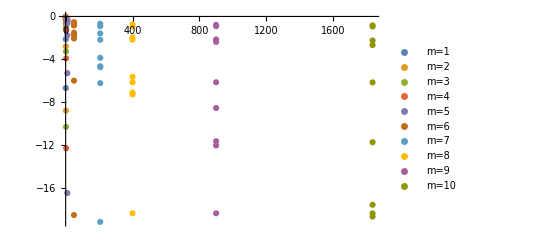

```mathematica
ListPlot[Table[simdiff2setM[[i]],{i,10}],PlotRange->All,PlotLegends->{"m=1","m=2","m=3","m=4","m=5","m=6","m=7","m=8","m=9","m=10"}]
```

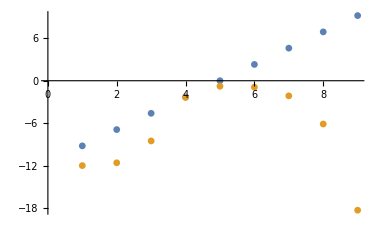

```mathematica
ListPlot[Transpose[simdiff2set[[9]]]]
```

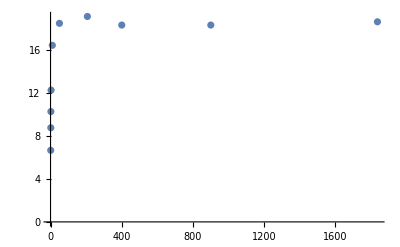

```mathematica
ListPlot[simdiff2setMM[[9]]]
```

FittedModel[18.7007 Erf[0.000813106 x]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 18.7007 | 0.985435 | 18.9771 | 6.15207×10^-8
b | 0.000813106 | 0.0000840302 | 9.67635 | 0.0000108456

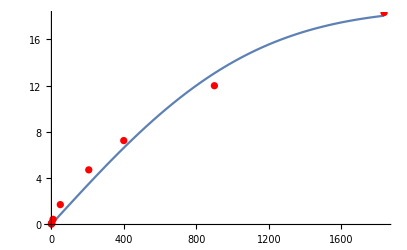

```mathematica
fitdiffexp1=NonlinearModelFit[simdiff2setMM[[1]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp1["ParameterTable"]
Show[{Plot[fitdiffexp1[x],{x,1,1836}],ListPlot[simdiff2setMM[[1]],PlotStyle->Red]}]
```

FittedModel[17.162 Erf[0.000887236 x]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 17.162 | 0.886075 | 19.3686 | 5.24133×10^-8
b | 0.000887236 | 0.0000931583 | 9.52395 | 0.0000122022

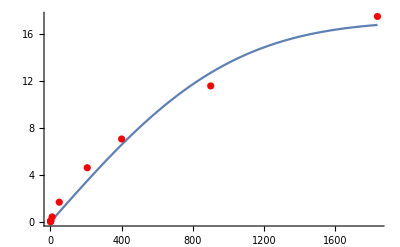

```mathematica
fitdiffexp2=NonlinearModelFit[simdiff2setMM[[2]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp2["ParameterTable"]
Show[{Plot[fitdiffexp2[x],{x,1,1836},PlotRange->All],ListPlot[simdiff2setMM[[2]],PlotStyle->Red,PlotRange->All]}]
```

FittedModel[11.3199 Erf[0.00111076 x]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 11.3199 | 0.61656 | 18.3598 | 7.97252×10^-8
b | 0.00111076 | 0.000133736 | 8.3056 | 0.0000333075

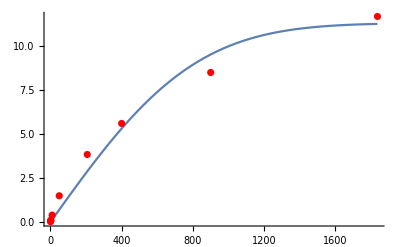

```mathematica
fitdiffexp3=NonlinearModelFit[simdiff2setMM[[3]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp3["ParameterTable"]
Show[{Plot[fitdiffexp3[x],{x,1,1836},PlotRange->All],ListPlot[fitdiffexp3[[3]],PlotStyle->Red,PlotRange->All]}]
```

FittedModel[2.42077 Erf[0.00316598 x]]

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.42077 | 0.139851 | 17.3096 | 1.26389×10^-7
b | 0.00316598 | 0.000565546 | 5.5981 | 0.000511378

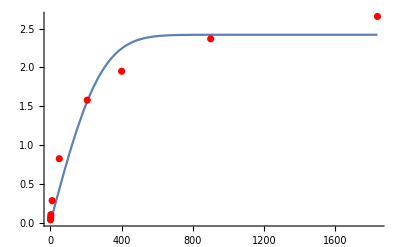

```mathematica
fitdiffexp4=NonlinearModelFit[simdiff2setMM[[4]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp4["ParameterTable"]
Show[{Plot[fitdiffexp4[x],{x,1,1836},PlotRange->All],ListPlot[simdiff2setMM[[4]],PlotStyle->Red,PlotRange->All]}]
```

FittedModel[0.710731 Erf[0.0485561 x]]

General::munfl: Exp[-1909.73] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7947.53] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.710731 | 0.0398005 | 17.8574 | 9.90679×10^-8
b | 0.0485561 | 0.0129263 | 3.75638 | 0.00557309

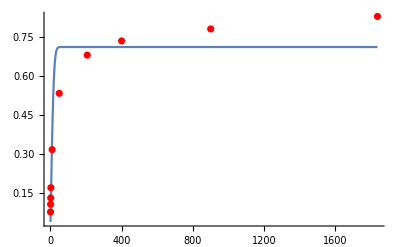

```mathematica
fitdiffexp5=NonlinearModelFit[simdiff2setMM[[5]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp5["ParameterTable"]
Show[{Plot[fitdiffexp5[x],{x,1,1836},PlotRange->All],ListPlot[simdiff2setMM[[5]],PlotStyle->Red,PlotRange->All]}]
```

FittedModel[0.865808 Erf[0.170082 x]]

General::munfl: Exp[-1239.53] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4628.44] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-23431.5] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.865808 | 0.0376324 | 23.007 | 1.35171×10^-8
b | 0.170082 | 0.0286544 | 5.93562 | 0.00034754

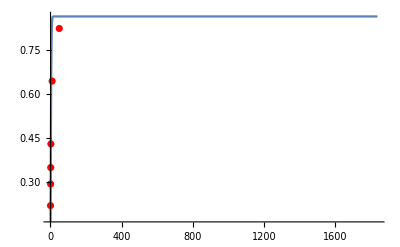

```mathematica
fitdiffexp6=NonlinearModelFit[simdiff2setMM[[6]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp6["ParameterTable"]
Show[{Plot[fitdiffexp6[x],{x,1,1836}],ListPlot[simdiff2setMM[[6]],PlotStyle->Red]}]
```

FittedModel[2.08146 Erf[0.234798 x]]

General::munfl: Exp[-2362.27] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-8820.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44655.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | 2.08146 | 0.0644386 | 32.3014 | 9.19395×10^-10
b | 0.234798 | 0.0246616 | 9.52079 | 0.0000122323

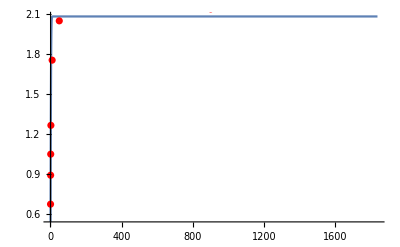

```mathematica
fitdiffexp7=NonlinearModelFit[simdiff2setMM[[7]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp7["ParameterTable"]
Show[{Plot[fitdiffexp7[x],{x,1,1836}],ListPlot[simdiff2setMM[[7]],PlotStyle->Red]}]
```

FittedModel[5.95548 Erf[0.262295 x]]

General::munfl: Exp[-2947.95] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11007.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-55726.8] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | 5.95548 | 0.147848 | 40.2811 | 1.58751×10^-10
b | 0.262295 | 0.0214863 | 12.2075 | 1.88106×10^-6

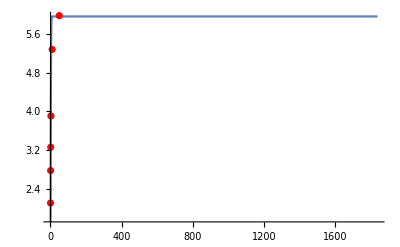

```mathematica
fitdiffexp8=NonlinearModelFit[simdiff2setMM[[8]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp8["ParameterTable"]
Show[{Plot[fitdiffexp8[x],{x,1,1836}],ListPlot[simdiff2setMM[[8]],PlotStyle->Red]}]
```

FittedModel[18.1515 Erf[0.273859 x]]

General::munfl: Exp[-3213.61] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-11999.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-60748.9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
a | 18.1515 | 0.416814 | 43.5483 | 8.52844×10^-11
b | 0.273859 | 0.0206009 | 13.2936 | 9.79129×10^-7

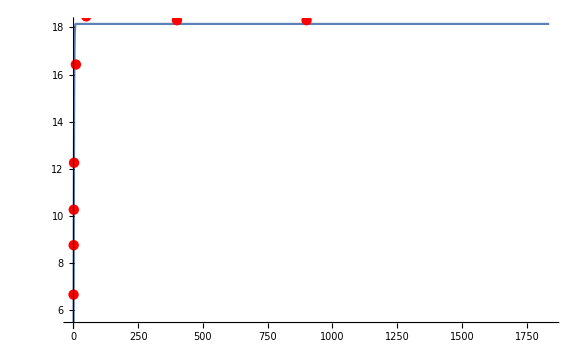

```mathematica
fitdiffexp9=NonlinearModelFit[simdiff2setMM[[9]],{a*Erf[b*x]},{a,b},x,Method->NMinimize]
fitdiffexp9["ParameterTable"]
Show[{Plot[fitdiffexp9[x],{x,1,1836}],ListPlot[simdiff2setMM[[9]],PlotStyle->Red]}]
```

```mathematica
fitdata={{a11,fitdiffexp1["BestFitParameters"][[1,2]],
b1,fitdiffexp1["BestFitParameters"][[2,2]]},
{a2,fitdiffexp2["BestFitParameters"][[1,2]],
b2,fitdiffexp2["BestFitParameters"][[2,2]]},
{a3,fitdiffexp3["BestFitParameters"][[1,2]],
b3,fitdiffexp3["BestFitParameters"][[2,2]]},
{a4,fitdiffexp4["BestFitParameters"][[1,2]],
b4,fitdiffexp4["BestFitParameters"][[2,2]]},
{a5,fitdiffexp5["BestFitParameters"][[1,2]],
b5,fitdiffexp5["BestFitParameters"][[2,2]]},
{a6,fitdiffexp6["BestFitParameters"][[1,2]],
b6,fitdiffexp6["BestFitParameters"][[2,2]]},
{a7,fitdiffexp7["BestFitParameters"][[1,2]],
b7,fitdiffexp7["BestFitParameters"][[2,2]]},
{a8,fitdiffexp8["BestFitParameters"][[1,2]],
b8,fitdiffexp8["BestFitParameters"][[2,2]]},
{a9,fitdiffexp9["BestFitParameters"][[1,2]],
b9,fitdiffexp9["BestFitParameters"][[2,2]]}};
```

```mathematica
Grid[fitdata,Frame->All]
```

a11 | 18.7007 | b1 | 0.000813106
a2 | 17.162 | b2 | 0.000887236
a3 | 11.3199 | b3 | 0.00111076
a4 | 2.42077 | b4 | 0.00316598
a5 | 0.710731 | b5 | 0.0485561
a6 | 0.865808 | b6 | 0.170082
a7 | 2.08146 | b7 | 0.234798
a8 | 5.95548 | b8 | 0.262295
a9 | 18.1515 | b9 | 0.273859

```mathematica
afit=Table[fitdata[[i]][[2]],{i,9}]
```

{18.7007,17.162,11.3199,2.42077,0.710731,0.865808,2.08146,5.95548,18.1515}

```mathematica
bfit=Table[fitdata[[i]][[4]],{i,9}]
```

{0.000813106,0.000887236,0.00111076,0.00316598,0.0485561,0.170082,0.234798,0.262295,0.273859}

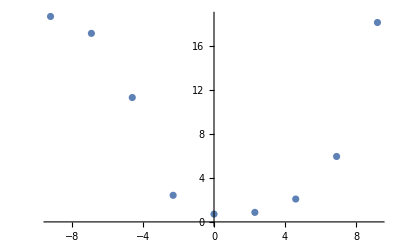

```mathematica
ListPlot[Transpose[{logo,afit}]]
```

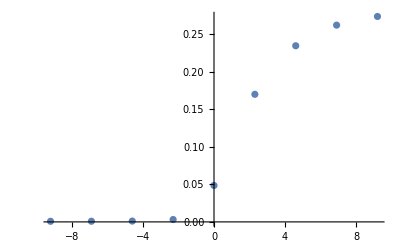

```mathematica
ListPlot[Transpose[{logo,bfit}]]
```

FittedModel[0.224387 (-0.928393+x)^2]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.224387 | 0.021801 | 10.2925 | 0.0000176857
b | 0.928393 | 0.395083 | 2.34987 | 0.0510974

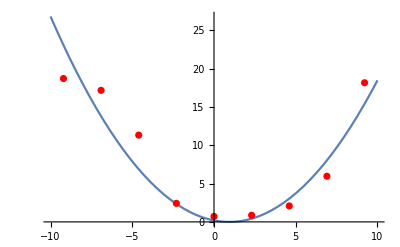

```mathematica
fitfita=NonlinearModelFit[Transpose[{logo,afit}],{a*(x-b)^2},{a,b},x,Method->NMinimize]
fitfita["ParameterTable"]
Show[{Plot[fitfita[x],{x,-10,10}],ListPlot[Transpose[{logo,afit}],PlotStyle->Red]}]
```

FittedModel[0.266983/(1+ⅇ^(-0.833364 («1»)))]

| Estimate | Standard Error | t-Statistic | P-Value
aa | 0.266983 | 0.00444389 | 60.0788 | 1.42917×10^-9
bb | 0.833364 | 0.0648106 | 12.8585 | 0.0000135993
c | 1.73388 | 0.109923 | 15.7736 | 4.11665×10^-6

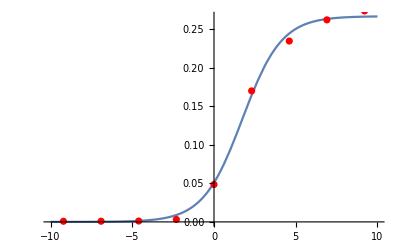

```mathematica
fitfitb=NonlinearModelFit[Transpose[{logo,bfit}],{aa/(1+Exp[-bb *(x-c)])},{aa,bb,c},x,Method->NMinimize]
fitfitb["ParameterTable"]
Show[{Plot[fitfitb[x],{x,-10,10}],ListPlot[Transpose[{logo,bfit}],PlotStyle->Red]}]
```

FittedModel[0.110618+0.133361 Erf[0.259645 x]]

| Estimate | Standard Error | t-Statistic | P-Value
aa | -0.133361 | 0.0184682 | -7.22112 | 0.000357555
bb | -0.259645 | 0.110755 | -2.34431 | 0.0575037
c | 0.110618 | 0.0117857 | 9.3858 | 0.000083042

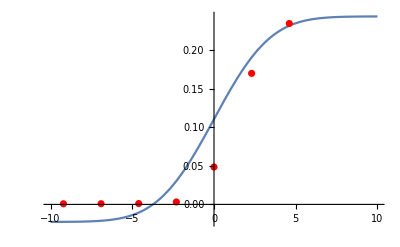

```mathematica
fitfitb2=NonlinearModelFit[Transpose[{logo,bfit}],{aa*Erf[bb*x]+c},{aa,bb,c},x,Method->NMinimize]
fitfitb2["ParameterTable"]
Show[{Plot[fitfitb2[x],{x,-10,10}],ListPlot[Transpose[{logo,bfit}],PlotStyle->Red]}]
```

FittedModel[0.349075 ⅇ^(1.01894 (-1.59591+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.349075 | 1.91999 | 0.181811 | 0.856154
b | 1.01894 | 0.815659 | 1.24923 | 0.214933
c | -1.59591 | 0.682915 | -2.33692 | 0.0217406

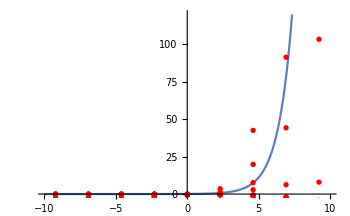

```mathematica
fitdiff=NonlinearModelFit[simdiff2data,{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fitdiff["ParameterTable"]
Show[{Plot[fitdiff[x],{x,-10,10}],ListPlot[simdiff2data,PlotStyle->Red]}]
```

FittedModel[-0.560205 ⅇ^(0.384183 (-3.93844+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.560205 | 0.0352156 | -15.9079 | 3.91659×10^-6
b | 0.384183 | 0.0133316 | 28.8175 | 1.15652×10^-7
c | -3.93844 | 0.00757914 | -519.642 | 3.42809×10^-15

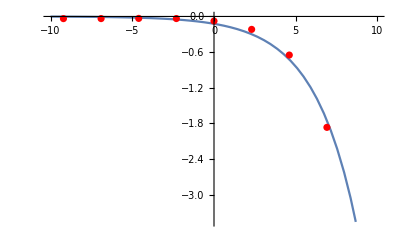

```mathematica
fitdiff1=NonlinearModelFit[simdiff2set[[1]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fitdiff1["ParameterTable"]
Show[{Plot[fitdiff1[x],{x,-10,10}],ListPlot[simdiff2set[[1]],PlotStyle->Red]}]
```

FittedModel[0.0000331414 ⅇ^(3.54915 (-5.71928+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0000331414 | 0.0308529 | 0.00107417 | 0.999178
b | 3.54915 | 266.666 | 0.0133093 | 0.989813
c | -5.71928 | 3.62905×10^-6 | -1.57597×10^6 | 4.40566×10^-36

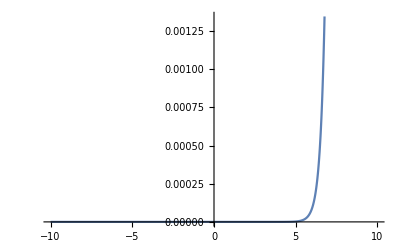

```mathematica
fitdiff5=NonlinearModelFit[simdiff2set[[5]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fitdiff5["ParameterTable"]
Show[{Plot[fitdiff5[x],{x,-10,10}],ListPlot[simdiff2set[[5]],PlotStyle->Red]}]
```

FittedModel[0.53833 ⅇ^(1.00442 (-0.227602+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.53833 | 0.0414925 | 12.9741 | 0.0000129088
b | 1.00442 | 0.0111137 | 90.377 | 1.23629×10^-10
c | -0.227602 | 0.0224355 | -10.1447 | 0.0000533603

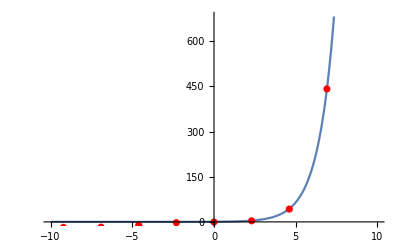

{90,2}

```mathematica
fitdiff10=NonlinearModelFit[simdiff2set[[10]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fitdiff10["ParameterTable"]
Show[{Plot[fitdiff10[x],{x,-10,10}],ListPlot[simdiff2set[[10]],PlotStyle->Red]}]
```

```mathematica
simdiff2set[[10]]//Dimensions
```

{9,2}

FittedModel[0.905794 ⅇ^(0.999518 (-0.58957+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.905794 | 0.00107341 | 843.851 | 5.15954×10^-172
b | 0.999518 | 0.000250725 | 3986.51 | 1.1178×10^-230
c | -0.58957 | 0.000971816 | -606.668 | 1.50952×10^-159

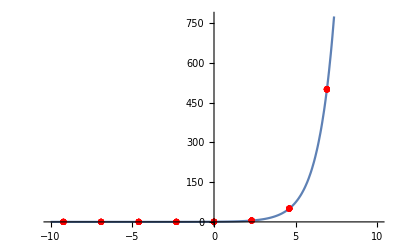

```mathematica
(********************************* Fitting: Subscript[m, p]-excluded exponents *****************************)
fitEX=NonlinearModelFit[dataEX,{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fitEX["ParameterTable"]
Show[{Plot[fitEX[x],{x,-10,10}],ListPlot[dataEX,PlotStyle->Red]}]
```

FittedModel[0.909796 ⅇ^(0.998687 (-0.585954+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.909796 | 0.000548632 | 1658.3 | 3.24583×10^-18
b | 0.998687 | 0.000127945 | 7805.57 | 2.98452×10^-22
c | -0.585954 | 0.000498487 | -1175.46 | 2.55884×10^-17

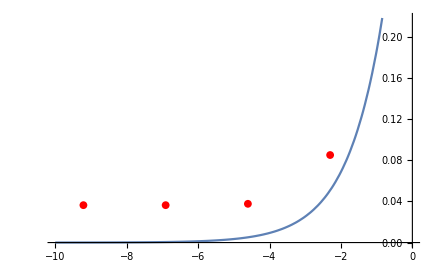

```mathematica
(* mp=1 *)
fit1EX=NonlinearModelFit[setEX[[1]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fit1EX["ParameterTable"]
Show[{Plot[fit1EX[x],{x,-10,0}],ListPlot[setEX[[1]],PlotStyle->Red]}]
```

FittedModel[0.904432 ⅇ^(0.999662 (-0.589456+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.904432 | 0.000195481 | 4626.69 | 6.88143×10^-21
b | 0.999662 | 0.0000456725 | 21887.6 | 6.13921×10^-25
c | -0.589456 | 0.00017674 | -3335.16 | 4.90458×10^-20

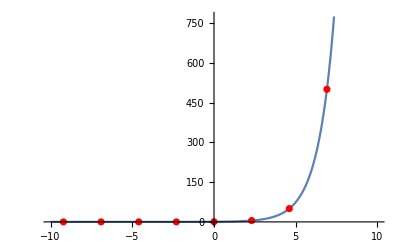

```mathematica
(* mp=10 *)
fit5EX=NonlinearModelFit[setEX[[5]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fit5EX["ParameterTable"]
Show[{Plot[fit5EX[x],{x,-10,10}],ListPlot[setEX[[5]],PlotStyle->Red]}]
```

FittedModel[0.903536 ⅇ^(0.999989 (-0.59161+x))]

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.903536 | 0.000027671 | 32652.8 | 5.569×10^-26
b | 0.999989 | 6.46922×10^-6 | 154576. | 4.94817×10^-30
c | -0.59161 | 0.0000250014 | -23663.1 | 3.84484×10^-25

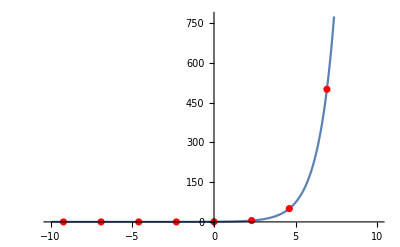

```mathematica
(* mp=1836 *)
fit10EX=NonlinearModelFit[setEX[[10]],{a*Exp[b *(x+c)]},{a,b,c},x,Method->NMinimize]
fit10EX["ParameterTable"]
Show[{Plot[fit10EX[x],{x,-10,10}],ListPlot[setEX[[10]],PlotStyle->Red]}]
```

```mathematica
(********************************* Percentage Error for Subscript[m, p]-excluded fitting *****************************)
```

```mathematica
b1=0.9;
b2=1;
b3=-0.58;
exp[x_]:=b1*Exp[b2 *(x+b3)];
expdata=Table[exp[logo[[i]]],{i,9}];
pererr=Table[Abs[expdata[[j]]-m[i][[j]]/massP[[i]]]/(m[i][[j]]/massP[[i]])*100,{i,10},{j,9}];
expfinal=Table[expdata[[j]]*massP[[i]],{i,10},{j,9}];
pererr2=Table[Abs[expfinal[[i]][[j]]-m[i][[j]]]/(m[i][[j]])*100,{i,10},{j,9}];
pererrdataM=FlattenAt[pererr2,{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10}}];
```

```mathematica
HFdata={-95.09233475330778,-78.20800717183442,-44.355360537235065,163.4754793017628,0.6536050413604295,0.0343941186073057,0.0008123876494092676,0.0003218729250466745,0.0010450768897157605,-98.71519751394369,-78.78228663145295,-43.36824032878961,-107.14964106493163,0.5816334409768267,0.02630315592181634,0.00041969408428598604,0.0004217595527713193,0.001099224418319952,-97.89720655922925,-77.99398655108388,-42.479794116082324,-49.497863113127885,0.5099490351464357,0.01997704999950218,0.0001827376815065223,0.0005186773122704477,0.0011468706289261043,-98.22308025476094,-80.16278253446617,-41.59307304506139,-27.615061919521043,0.39699147000720736,0.011955774475352449,9.709368907126533*^-6,0.0006804980142286082,0.0012190470931054487,-94.96907974740486,-75.10357534569012,-35.695894021448964,-9.78377083133682,0.12338767179158935,0.0007249665476911393,0.0004782987476882835,0.0011471505896218476,0.0013960714848485684,-95.05100332264685,-62.29846407117392,-23.64539908033238,-2.5299127065567846,0.00788505851649141,0.0005775618764185545,0.0012626519537430824,0.0014414158481351619,0.0014928644522674284,-80.61049224752996,-46.247633721381106,-12.23474544786353,-0.4834008775866077,0.0000671348693656443,0.0013663320202213745,0.0014936410241132478,0.0015108148723321467,0.0015144187153052855,-72.5690137164316,-38.461883030081154,-7.986866011611875,-0.18371877847640836,0.0007685843005395437,0.0015327074615164387,0.0015326692448036727,0.0015219817292752244,0.0015178388672356094,-62.55489266813158,-28.82365109280358,-4.173643469094685,-0.045287688381120156,0.0016459425846295007,0.0016398916108191096,0.00155649099175089,0.001528709896590851,0.0015198917147018797,-53.65741707679378,-20.899615170026916,-2.0836451046648894,-0.010109569967183502,0.0021361201562796165,0.0016857197595617054,0.0015663483775468774,0.0015314716858513,0.0015207322091694347};
```

```mathematica
alldata=Table[{dataMo[[i,1]],Flatten[expfinal][[i]],dataM[[i,2]],pererrdataM[[i]],HFdata[[i]]},{i,90}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["all_data_1s_HF.xlsx",alldata]
```

all_data_1s_HF.xlsx

```mathematica
HFdata//TableForm
```

-95.0923
-78.208
-44.3554
163.475
0.653605
0.0343941
0.000812388
0.000321873
0.00104508
-98.7152
-78.7823
-43.3682
-107.15
0.581633
0.0263032
0.000419694
0.00042176
0.00109922
-97.8972
-77.994
-42.4798
-49.4979
0.509949
0.019977
0.000182738
0.000518677
0.00114687
-98.2231
-80.1628
-41.5931
-27.6151
0.396991
0.0119558
9.70937×10^-6
0.000680498
0.00121905
-94.9691
-75.1036
-35.6959
-9.78377
0.123388
0.000724967
0.000478299
0.00114715
0.00139607
-95.051
-62.2985
-23.6454
-2.52991
0.00788506
0.000577562
0.00126265
0.00144142
0.00149286
-80.6105
-46.2476
-12.2347
-0.483401
0.0000671349
0.00136633
0.00149364
0.00151081
0.00151442
-72.569
-38.4619
-7.98687
-0.183719
0.000768584
0.00153271
0.00153267
0.00152198
0.00151784
-62.5549
-28.8237
-4.17364
-0.0452877
0.00164594
0.00163989
0.00155649
0.00152871
0.00151989
-53.6574
-20.8996
-2.08365
-0.0101096
0.00213612
0.00168572
0.00156635
0.00153147
0.00152073